```mathematica
fileName = "/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json";
RadioButtonBar[
Dynamic[fileName],
{
"/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json",
"~/Downloads/optimizerHistory.json"
},Appearance->"Vertical"]
```

| /Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json
 | ~/Downloads/optimizerHistory.json

```mathematica
raw=Import[fileName];

raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

```mathematica
(*Optional: Drop rows with non-numeric values*)
(*Length[raw]
raw = Select[raw,AllTrue[Values[#],NumericQ]&];
Length[raw]*)
```

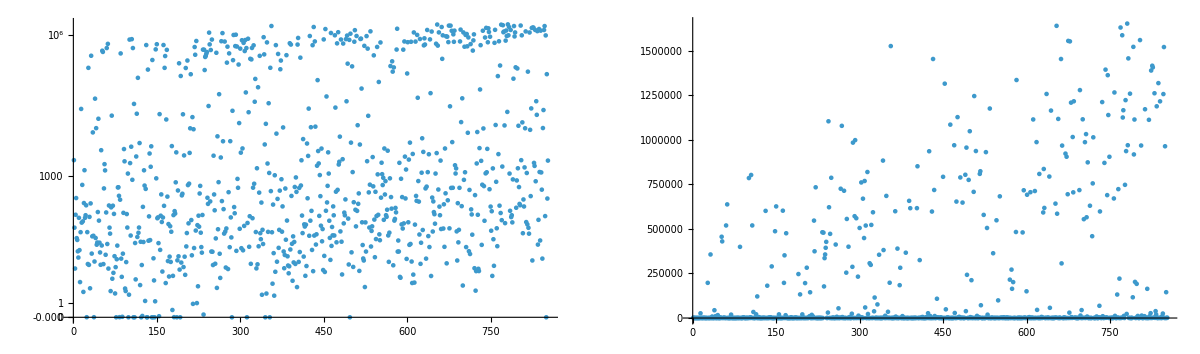

```mathematica
GraphicsGrid[{{
ListPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->All,
Joined->False,
ImageSize->600,
ScalingFunctions->"SignedLog"
],
ListPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{0,All},
Joined->False,
ImageSize->600
]
}},ImageSize->1200]
```

### Live plot

```mathematica
(*Dynamic[livePlot]

makeLivePlot[]:=(
raw=Import[fileName];

raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];

livePlot = GraphicsGrid[{{
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->All,
Joined->False,
ImageSize->600
],
ListPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{0,All},
Joined->False,
ImageSize->600
]
}},ImageSize->1200];
)

task=CreateScheduledTask[makeLivePlot[],1]; (*Runs myFunction every 1 second*)
StartScheduledTask[task];*)
```

### Analyze

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]];
```

```mathematica
(*Format for yml*)
string = "";
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
];
string
```

L1PhaseSet : -29.8468028109
L2PhaseSet : -40.4676460034
S1ELkG : 209.0684650767
S2ELkG : -2247.9176927407
S3ELkG : -1401.8165327565
S1EL_xOffset : -0.000639576
S1EL_yOffset : -0.0034613661
S2EL_xOffset : -0.0033192194
S2EL_yOffset : -0.0024896306
S2ER_xOffset : -0.0018343582
S2ER_yOffset : -0.0012995615
S1ER_xOffset : 0.000291516
S1ER_yOffset : -0.0009120653
PDrive_median_x : 4.7724e-6
PDrive_median_y : -1.1793e-6
PDrive_median_xp : 2.7346e-6
PDrive_median_yp : 3.9944e-6
PDrive_median_energy : 9.974220211672054291e9
PDrive_sigmaSI90_x : 0.0000547349
PDrive_sigmaSI90_y : 0.0000157451
PDrive_sigmaSI90_z : 4.9369e-6
PDrive_sigmaSI90_xp : 0.0001196902
PDrive_sigmaSI90_yp : 0.000083459
PDrive_sigmaSI90_energy : 3.1477359080489889e7
PDrive_emitSI90_x : 0.0000965735
PDrive_emitSI90_y : 0.0000207996
PDrive_norm_emit_x : 0.0000394735
PDrive_norm_emit_y : 7.5301e-6
PDrive_charge_nC : 1.59984
PDrive_BMAG_x : 1.3679963818
PDrive_BMAG_y : 1.3315399949
PDrive_sliced_BMAG_x : List(2.4624630657,1.7049206288,1.4432308621,1.9496086666,3.0881336129)
PDrive_sliced_BMAG_y : List(1.8609445676,1.6485461202,1.4411702287,1.5211146928,1.0837548615)
lostChargeFraction : 0.0001
errorTerm_lostChargeFraction : 0.
errorTerm_bunchSpacing : 0
errorTerm_transverseOffset : 0.
errorTerm_angleOffset : 0.
errorTerm_mainObjective : 0.
errorTerm_secondaryObjective : 5.447e-6
maximizeMe : 1.6522895975767411e6
inputBeamFilePathSuffix : "/beams/2024-10-22_Impact_OneBunch/2024-10-22_oneBunch.h5"
csrTF : True

```mathematica
(*Not tested to be robust... beware!*)
indepVarKeys = Keys[raw[[1]]][[1;;(Position[Keys[raw[[1]]],"PDrive_median_x"][[1,1]]-1)]]
```

{L1PhaseSet,L2PhaseSet,S1ELkG,S2ELkG,S3ELkG,S1EL_xOffset,S1EL_yOffset,S2EL_xOffset,S2EL_yOffset,S2ER_xOffset,S2ER_yOffset,S1ER_xOffset,S1ER_yOffset}

## Plot specific

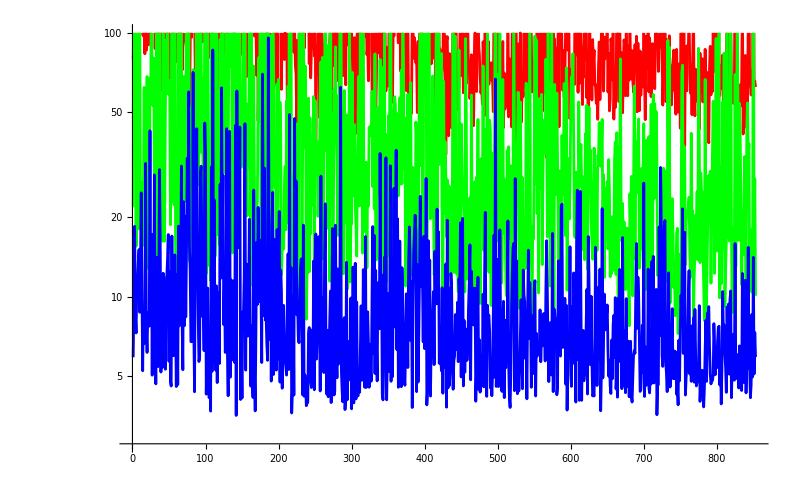

```mathematica
keys = {"PDrive_sigmaSI90_x","PDrive_sigmaSI90_y","PDrive_sigmaSI90_z","PWitness_sigmaSI90_x","PWitness_sigmaSI90_y","PWitness_sigmaSI90_z"};
ListLogPlot[
(10^6 raw[[All,#]]&/@keys)~Join~{(10^6 Max[#]&/@raw[[All,keys]])},
Joined->True,
ImageSize->800,
PlotStyle->{{Red},{Green},{Blue},{Red,Dashed},{Green,Dashed},{Blue,Dashed},{Black}},
InterpolationOrder->1,
PlotRange->{All,100}
]
(*ListPlot[
raw[[All,#]]&/@{"PWitness_sigmaSI90_x","PWitness_sigmaSI90_y","PWitness_sigmaSI90_z"},
Joined->True
]*)
```

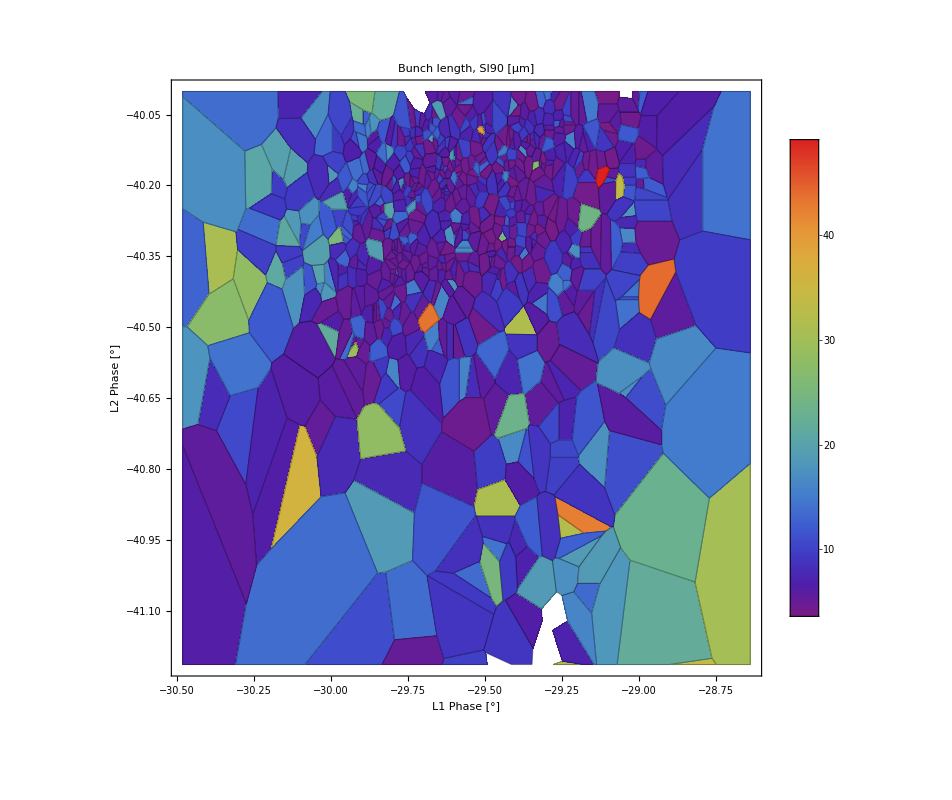

```mathematica
ListDensityPlot[{
#["L1PhaseSet"],
#["L2PhaseSet"],
10^6#["PDrive_sigmaSI90_z"]
(*10^6 Max[{#["PDrive_sigmaSI90_z"],#["PWitness_sigmaSI90_z"]}]*)
}&/@raw,ImageSize->800,
ColorFunction->"Rainbow",InterpolationOrder->0,PlotRange->{All,50},Mesh->All,ColorFunction->"Rainbow",PlotLegends->Automatic,FrameLabel->{"L1 Phase [°]","L2 Phase [°]"},PlotLabel->"Bunch length, SI90 [μm]",LabelStyle->20]
```

```mathematica
ListDensityPlot[{
#["L1PhaseSet"],
#["L2PhaseSet"],
10^6 Max[{#["PDrive_sigmaSI90_z"],#["PWitness_sigmaSI90_z"]}]
}&/@raw,ImageSize->800,
ColorFunction->"Rainbow",InterpolationOrder->0,PlotRange->{All,50},Mesh->All,ColorFunction->"Rainbow",PlotLegends->Automatic]
```

-Graphics-

```mathematica
(*toPlot = {
#["L1PhaseSet"],
#["L2PhaseSet"]
}&/@raw[[1;;-1;;10]];
colors = Table[ColorData["Rainbow"][Rescale[i,{1,Length[toPlot]}]],{i,Length[toPlot]}];

ListPlot[{#}&/@toPlot,
ImageSize->800,
FrameLabel->{"L1 Phase [°]","L2 Phase [°]"},
LabelStyle->20,
Frame->True,
PlotStyle->colors,
PlotLabel->"Iteration number = color; later iterations are more red",
PlotMarkers->{Graphics[Disk[]],0.01}
]*)
```

```mathematica
(*Show[
ListContourPlot3D[
{
#["S1ELkG"],
#["S2ELkG"],
#["S3ELkG"],
(10^6#["PDrive_sigmaSI90_z"])
}&/@raw,
PlotLegends->Automatic,
ImageSize->800,
SphericalRegion->True,
Contours->{4,4.9,5,5.1,6}
],
ListPointPlot3D[
{
#["S1ELkG"],
#["S2ELkG"],
#["S3ELkG"]
}&/@raw
]
]*)
```

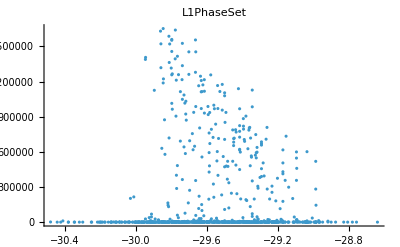
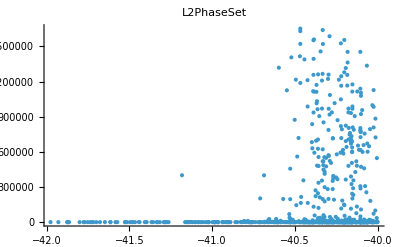
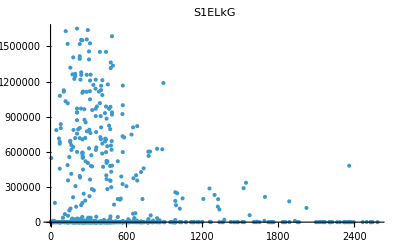
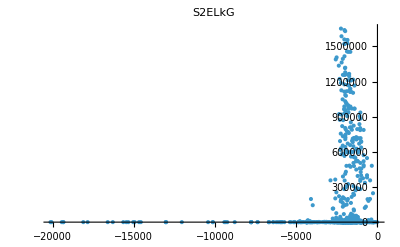
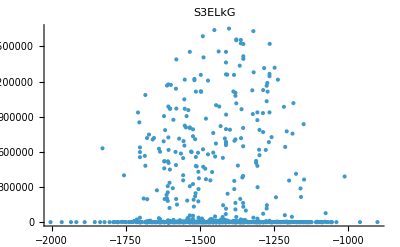
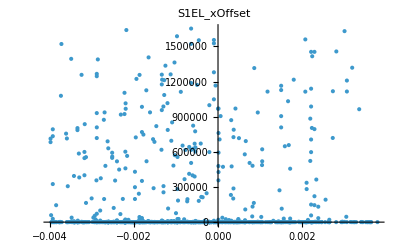
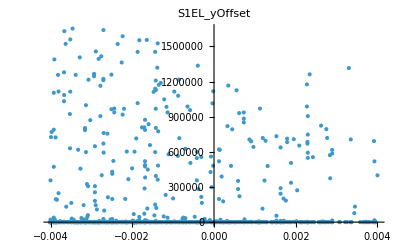
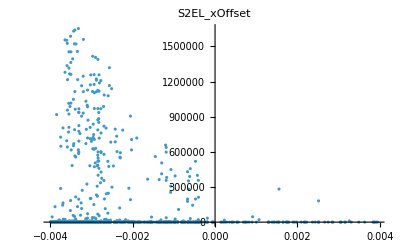
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | 0 | 0 | 0

```mathematica
imgArr=ParallelTable[
ListPlot[
{#[key],#["maximizeMe"]}&/@raw,
PlotLabel->key,
ImageSize->400,
LabelStyle->15,
PlotRange->All
],
{key,indepVarKeys}
];

displayCols = 4;
Grid[
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
],
Frame->All
]
```

## Plot all

```mathematica
(*This block can get really slow for large numbers of simulations; pare down number of points to plot*)
shotCount = Length[raw[[All,1]]];
indicesToPlot = DeleteDuplicates[Round[Range[1,shotCount,shotCount/1000]]];
```

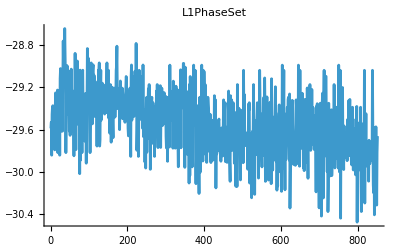
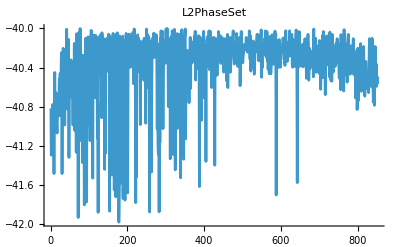
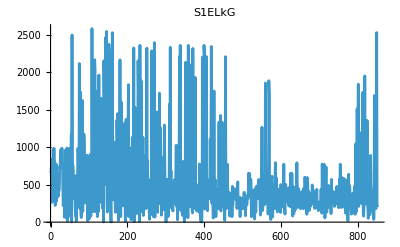
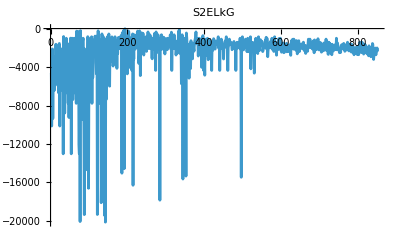
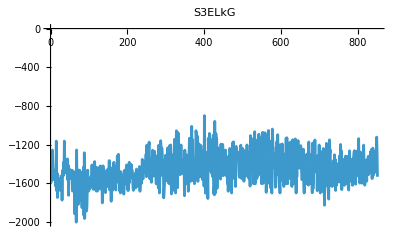
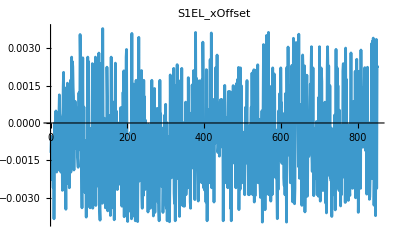
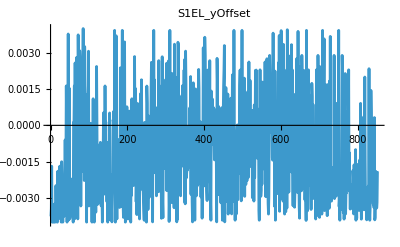
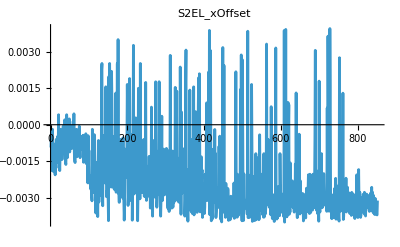
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | 0

```mathematica
imgArr=ParallelTable[
ListPlot[
raw[[indicesToPlot,key]],
PlotLabel->key,
ImageSize->400,
LabelStyle->15,
PlotRange->All,
Joined->True
],
{key,Keys[raw[[1]]]}
];

displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm
```

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
Export[
"~/srData.csv",
Dataset[raw]
]
```

~/srData.csv

## Linear model fit

```mathematica
freeVars=Intersection[
Keys[raw[[1]]],
{"QA10361kG","QA10371kG","QE10425kG","QE10441kG","QE10511kG","QE10525kG","L0BPhaseSet","L1PhaseSet","L2PhaseSet","L3PhaseSet","Q1EkG","Q2EkG","Q3EkG","Q4EkG","Q5EkG","Q6EkG","S1ELkG","S2ELkG","S3ELkG","S3ERkG","S2ERkG","S1ERkG","S1EL_xOffset","S1EL_yOffset","S2EL_xOffset","S2EL_yOffset","S2ER_xOffset","S2ER_yOffset","S1ER_xOffset","S1ER_yOffset","Q5FFkG","Q4FFkG","Q3FFkG","Q2FFkG","Q1FFkG","Q0FFkG", "XC1FFkG","XC3FFkG","YC1FFkG","YC2FFkG"}
]
(*Mathematica doesn't like underscores...*)
freeVarsMathematica=StringReplace[#,"_"->""]&/@freeVars;
```

{L1PhaseSet,L2PhaseSet,S1ELkG,S1EL_xOffset,S1EL_yOffset,S1ER_xOffset,S1ER_yOffset,S2ELkG,S2EL_xOffset,S2EL_yOffset,S2ER_xOffset,S2ER_yOffset,S3ELkG}

```mathematica
fitVar = "PDrive_twiss_beta_x"
(*fitVar = "bunchSpacing"*)
```

PDrive_twiss_beta_x

```mathematica
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
]
```

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

```mathematica
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"Actual","Predicted"}
]
```

-Graphics-

```mathematica
lm["ANOVATable"]
```

### Fit all dependent vars

```mathematica
allFitVars  = Complement[
Keys[raw[[1]]],
freeVars
];
```

```mathematica
(*
imgArr=Table[
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
];

Show[
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
Frame->True,
FrameLabel->{"Actual","Predicted"},
PlotLabel->Row[{fitVar,": ",Style[ToString[lm["RSquared"]],ColorData["Rainbow"][lm["RSquared"]]]}],
ImageSize->400,
AspectRatio->1,
LabelStyle->15,
PlotRange->All
],
Plot[x,{x,Min[lm["Response"]],Max[lm["Response"]]},PlotStyle->Red]
],
{fitVar,allFitVars}
];*)
```

```mathematica
(*displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm*)
```

## Parse JSON strings to assoc

```mathematica
(*This is a stupid trick, but ensures numbers in scientific notation are interpreted correctly: https://mathematica.stackexchange.com/questions/15051/reading-in-scientific-notation-from-c-to-mathematica*)
stringToNumber[string_]:=ImportString[string,"Table"][[1,1]]
```

```mathematica
jsonTextToAssoc[string_]:=(
stringParts = StringSplit[StringDelete[#,WhitespaceCharacter],":"]&/@StringSplit[string,"\n"];
Association[#[[1]]->stringToNumber[#[[2]]]&/@stringParts]
)
```

```mathematica
tmp="L0BPhaseSet : -1.7210344516
L1PhaseSet : -20.3120443443
L2PhaseSet : -38.6737055166
L3PhaseSet : -1.4632882388
S1EL_xOffset : 0.0003852549
S1EL_yOffset : -0.0002411137
S2EL_xOffset : -0.0014178669
S2EL_yOffset : 0.0000111705
S2ER_xOffset : -0.002238162
S2ER_yOffset : -0.0006759962
S1ER_xOffset : 0.0010071369
S1ER_yOffset : 0.0003984557
XC1FFkG : 0.2064553639
XC3FFkG : -0.089916372
YC1FFkG : -0.0022311951
YC2FFkG : -0.0085115845";
```

```mathematica
priorSettings = jsonTextToAssoc[tmp]
```

<|L0BPhaseSet→-1.72103,L1PhaseSet→-20.312,L2PhaseSet→-38.6737,L3PhaseSet→-1.46329,S1EL_xOffset→0.000385255,S1EL_yOffset→-0.000241114,S2EL_xOffset→-0.00141787,S2EL_yOffset→0.0000111705,S2ER_xOffset→-0.00223816,S2ER_yOffset→-0.000675996,S1ER_xOffset→0.00100714,S1ER_yOffset→0.000398456,XC1FFkG→0.206455,XC3FFkG→-0.0899164,YC1FFkG→-0.0022312,YC2FFkG→-0.00851158|>

```mathematica
TableForm[
Table[
{
key,priorSettings[key],bestCase[key],bestCase[key]-priorSettings[key]
},
{key,Keys[priorSettings]}
],
TableHeadings->{None,{
Style["Parameter",Bold],
Style["150 μm spacing",Bold],
Style["New spacing",Bold],
Style["Delta",Bold]}}
]
```

Parameter | 150 μm spacing | New spacing | Delta
L0BPhaseSet | -1.72103 | Missing[KeyAbsent,L0BPhaseSet] | 1.72103+Missing[KeyAbsent,L0BPhaseSet]
L1PhaseSet | -20.312 | -29.8468 | -9.53476
L2PhaseSet | -38.6737 | -40.4676 | -1.79394
L3PhaseSet | -1.46329 | Missing[KeyAbsent,L3PhaseSet] | 1.46329+Missing[KeyAbsent,L3PhaseSet]
S1EL_xOffset | 0.000385255 | -0.000639576 | -0.00102483
S1EL_yOffset | -0.000241114 | -0.00346137 | -0.00322025
S2EL_xOffset | -0.00141787 | -0.00331922 | -0.00190135
S2EL_yOffset | 0.0000111705 | -0.00248963 | -0.0025008
S2ER_xOffset | -0.00223816 | -0.00183436 | 0.000403804
S2ER_yOffset | -0.000675996 | -0.00129956 | -0.000623565
S1ER_xOffset | 0.00100714 | 0.000291516 | -0.000715621
S1ER_yOffset | 0.000398456 | -0.000912065 | -0.00131052
XC1FFkG | 0.206455 | Missing[KeyAbsent,XC1FFkG] | -0.206455+Missing[KeyAbsent,XC1FFkG]
XC3FFkG | -0.0899164 | Missing[KeyAbsent,XC3FFkG] | 0.0899164+Missing[KeyAbsent,XC3FFkG]
YC1FFkG | -0.0022312 | Missing[KeyAbsent,YC1FFkG] | 0.0022312+Missing[KeyAbsent,YC1FFkG]
YC2FFkG | -0.00851158 | Missing[KeyAbsent,YC2FFkG] | 0.00851158+Missing[KeyAbsent,YC2FFkG]